{}

{}

{}

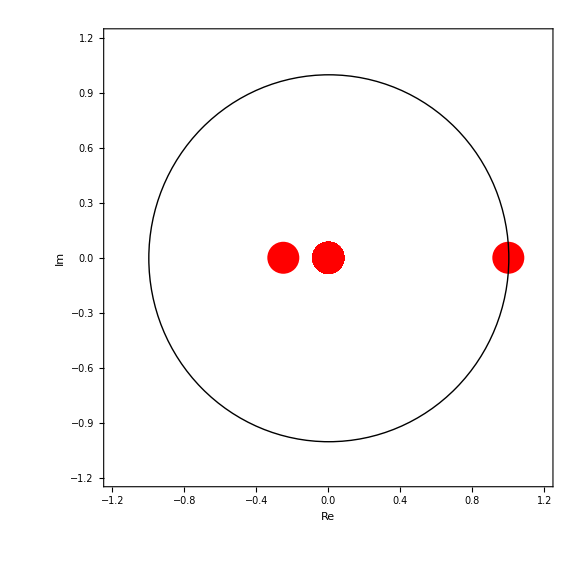

```mathematica
(*Implementation of the Projection Operators*)
projectC ={};
For[i = 0, i < 64,i++,
Clear[rowS];
rowS = {};
If[Not[OddQ[Quotient[i,8]]]&& Not[OddQ[i]],
For[j = 0, j < 64,j++,
If[j == i || j == (i+9),rowS = Append[rowS,1];,rowS = Append[rowS,0];]];,
For[j = 0, j < 64,j++,
rowS = Append[rowS,0];];
];
projectC= Append[projectC, rowS];
]
projectB ={};
For[i = 0, i < 64,i++,
Clear[rowS];
rowS = {};
If[Not[OddQ[Quotient[i,16]]]&& Not[OddQ[Quotient[i,2]]],
For[j = 0, j < 64,j++,
If[j == i || j == (i+18),rowS = Append[rowS,1];,rowS = Append[rowS,0];]];,
For[j = 0, j < 64,j++,
rowS = Append[rowS,0];];
];
projectB= Append[projectB, rowS];
]
projectA ={};
For[i = 0, i < 64,i++,
Clear[rowS];
rowS = {};
If[Not[OddQ[Quotient[i,32]]]&& Not[OddQ[Quotient[i,4]]],
For[j = 0, j < 64,j++,
If[j == i || j == (i+36),rowS = Append[rowS,1];,rowS = Append[rowS,0];]];,
For[j = 0, j < 64,j++,
rowS = Append[rowS,0];];
];
projectA= Append[projectA, rowS];
]

(*Implementation of the Hadamard operations*)

a =1/Sqrt[2];
b =1/Sqrt[2];
c =1/Sqrt[2];
d =-1/Sqrt[2];

had1 = {{a,0,0,0,b,0,0,0},{0,a,0,0,0,b,0,0},{0,0,a,0,0,0,b,0},{0,0,0,a,0,0,0,b},{c,0,0,0,d,0,0,0},{0,c,0,0,0,d,0,0},{0,0,c,0,0,0,d,0},{0,0,0,c,0,0,0,d}};
had2 = {{a,0,b,0,0,0,0,0},{0,a,0,b,0,0,0,0},{c,0,d,0,0,0,0,0},{0,c,0,d,0,0,0,0},{0,0,0,0,a,0,b,0},{0,0,0,0,0,a,0,b},{0,0,0,0,c,0,d,0},{0,0,0,0,0,c,0,d}} ;
had3 =  {{a,b,0,0,0,0,0,0},{c,d,0,0,0,0,0,0},{0,0,a,b,0,0,0,0},{0,0,c,d,0,0,0,0},{0,0,0,0,a,b,0,0},{0,0,0,0,c,d,0,0},{0,0,0,0,0,0,a,b},{0,0,0,0,0,0,c,d}};

(*Implementation of the Logic Functions*)

and13 = {{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0}};
and12 = {{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}};
and23 = {{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,1,0,0,0,0}};
xor13 ={{1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1}};
xor12 = {{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}};
xor23= {{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1}};
or12 = {{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}};
or23 = {{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1},{0,0,0,0,1,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0}};
or13 = {{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}};

not1 = {{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0}};
not2 = {{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0}} ;
not3 =  {{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}};

nand12 = and12.not3;
nand13 = and13.not2;
nand23 = and23.not1;

(*Creation of the related superoperator*)

ρnand12= Outer[Times,nand12,nand12];
Snand12 = {};
For[i= 1,i<9,i++,
For[k = 1,k<9,k++,
rowS = {};
For[j = 1,j<9,j++,
rowS = Append[rowS,Part[ρnand12,i,j,k]];];
rowS = Flatten[rowS];
Snand12 = Append[Snand12,rowS]]];
ρnand13= Outer[Times,nand13,nand13];
Snand13 = {};
For[i= 1,i<9,i++,
For[k = 1,k<9,k++,
rowS = {};
For[j = 1,j<9,j++,
rowS = Append[rowS,Part[ρnand13,i,j,k]];];
rowS = Flatten[rowS];
Snand13 = Append[Snand13,rowS]]];
ρnand23= Outer[Times,nand23,nand23];
Snand23 = {};
For[i= 1,i<9,i++,
For[k = 1,k<9,k++,
rowS = {};
For[j = 1,j<9,j++,
rowS = Append[rowS,Part[ρnand23,i,j,k]];];
rowS = Flatten[rowS];
Snand23 = Append[Snand23,rowS]]];


ρand12= Outer[Times,and12,and12];
Sand12 = {};
For[i= 1,i<9,i++,
For[k = 1,k<9,k++,
rowS = {};
For[j = 1,j<9,j++,
rowS = Append[rowS,Part[ρand12,i,j,k]];];
rowS = Flatten[rowS];
Sand12 = Append[Sand12,rowS]]];
ρand13= Outer[Times,and13,and13];
Sand13 = {};
For[i= 1,i<9,i++,
For[k = 1,k<9,k++,
rowS = {};
For[j = 1,j<9,j++,
rowS = Append[rowS,Part[ρand13,i,j,k]];];
rowS = Flatten[rowS];
Sand13 = Append[Sand13,rowS]]];
ρand23= Outer[Times,and23,and23];
Sand23 = {};
For[i= 1,i<9,i++,
For[k = 1,k<9,k++,
rowS = {};
For[j = 1,j<9,j++,
rowS = Append[rowS,Part[ρand23,i,j,k]];];
rowS = Flatten[rowS];
Sand23 = Append[Sand23,rowS]]];
ρxor13= Outer[Times,xor13,xor13];
Sxor13 = {}
For[i= 1,i<9,i++,
For[k = 1,k<9,k++,
rowS = {};
For[j = 1,j<9,j++,
rowS = Append[rowS,Part[ρxor13,i,j,k]];];
rowS = Flatten[rowS];
Sxor13 = Append[Sxor13,rowS]]];

ρxor12= Outer[Times,xor12,xor12];
Sxor12 = {}
For[i= 1,i<9,i++,
For[k = 1,k<9,k++,
rowS = {};
For[j = 1,j<9,j++,
rowS = Append[rowS,Part[ρxor12,i,j,k]];];
rowS = Flatten[rowS];
Sxor12 = Append[Sxor12,rowS]]];

ρxor23= Outer[Times,xor23,xor23];
Sxor23 = {}
For[i= 1,i<9,i++,
For[k = 1,k<9,k++,
rowS = {};
For[j = 1,j<9,j++,
rowS = Append[rowS,Part[ρxor23,i,j,k]];];
rowS = Flatten[rowS];
Sxor23 = Append[Sxor23,rowS]]];

ρor23= Outer[Times,or23,or23];
Sor23 = {};
For[i= 1,i<9,i++,
For[k = 1,k<9,k++,
rowS = {};
For[j = 1,j<9,j++,
rowS = Append[rowS,Part[ρor23,i,j,k]];];
rowS = Flatten[rowS];
Sor23 = Append[Sor23,rowS]]];

ρor12= Outer[Times,or12,or12];
Sor12 = {};
For[i= 1,i<9,i++,
For[k = 1,k<9,k++,
rowS = {};
For[j = 1,j<9,j++,
rowS = Append[rowS,Part[ρor12,i,j,k]];];
rowS = Flatten[rowS];
Sor12 = Append[Sor12,rowS]]];

ρor13= Outer[Times,or13,or13];
Sor13 = {};
For[i= 1,i<9,i++,
For[k = 1,k<9,k++,
rowS = {};
For[j = 1,j<9,j++,
rowS = Append[rowS,Part[ρor13,i,j,k]];];
rowS = Flatten[rowS];
Sor13 = Append[Sor13,rowS]]];

ρhad1= Outer[Times,had1,Conjugate[had1]];
Shad1 = {};
For[i= 1,i<9,i++,
For[k = 1,k<9,k++,
rowS = {};
For[j = 1,j<9,j++,
rowS = Append[rowS,Part[ρhad1,i,j,k]];];
rowS = Flatten[rowS];
Shad1 = Append[Shad1,rowS]]];

ρhad2= Outer[Times,had2,Conjugate[had2]];
Shad2 = {};
For[i= 1,i<9,i++,
For[k = 1,k<9,k++,
rowS = {};
For[j = 1,j<9,j++,
rowS = Append[rowS,Part[ρhad2,i,j,k]];];
rowS = Flatten[rowS];
Shad2 = Append[Shad2,rowS]]];

ρhad3= Outer[Times,had3,Conjugate[had3]];
Shad3= {};
For[i= 1,i<9,i++,
For[k = 1,k<9,k++,
rowS = {};
For[j = 1,j<9,j++,
rowS = Append[rowS,Part[ρhad3,i,j,k]];];
rowS = Flatten[rowS];
Shad3 = Append[Shad3,rowS]]];

(*Implementation of different wirings*)

cycOrXorOr = Sor23.Shad3.projectA.Sxor13.Shad1.projectB.Sor12.Shad2.projectC;
cycXorXorXor = Sxor23.Shad3.projectA.Sxor13.Shad1.projectB.Sxor12.Shad2.projectC;
cycAndXorOr = Sor23.Shad3.projectA.Sxor13.Shad1.projectB.Sand12.Shad2.projectC;
cycAndXorOr2 = Sxor13.Shad1.projectB.Sand12.Shad2.projectC.Sor23.Shad3.projectA;
cycAndAndAnd = Sand23.Shad3.projectA.Sand13.Shad1.projectB.Sand12.Shad2.projectC;
cycNandNandNand = Snand23.Shad3.projectA.Snand13.Shad1.projectB.Snand12.Shad2.projectC;
cycOrOrOr = Sor23.Shad3.projectA.Sor13.Shad1.projectB.Sor12.Shad2.projectC;
cyc =cycAndXorOr2;

(*Plot the resulting eigenvalues*)

p = ListPlot[{Re[#],Im[#]}&/@Eigenvalues[cyc],AxesOrigin->{0,0},PlotRange->{{-1.2,1.2},{-1.2,1.2}},AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,None}},PlotStyle->Directive[Red,PointSize[.04]],LabelStyle->{FontFamily->"CMU Serif",FontSize->30},ImageSize->Large];
Show[p,Graphics[{Thick,Circle[{0,0},1]}]]
```